```mathematica
generateKeyWithPlot[seed_Integer]:=Module[{G=4 π^2,conv=1/(1.496*^8*365.25*24*3600),pos1,vel1,pos2,vel2,pos3,vel3,q2x,q2y,q3x,q3y,m1=1,m2=1,m3=1,eq,init,sol,traj1,traj2,traj3,timeSteps,positions,keyData,binaryKeyData,key},
(*Initial conditions*)
pos1={0,0};
vel1={0,10}*conv;
SeedRandom[seed];
q2x=RandomReal[{5,20}];q2y=RandomReal[{0,10}];
pos2={q2x,q2y};vel2={-10,0}*conv;
q3x=RandomReal[{-10,0}];q3y=RandomReal[{5,20}];
pos3={q3x,q3y};vel3={0,0};

(*Differential equations*)eq={
x1''[t]==G m2 (x2[t]-x1[t])/Norm[{x2[t]-x1[t],y2[t]-y1[t]}]^3+G m3 (x3[t]-x1[t])/Norm[{x3[t]-x1[t],y3[t]-y1[t]}]^3,y1''[t]==G m2 (y2[t]-y1[t])/Norm[{x2[t]-x1[t],y2[t]-y1[t]}]^3+G m3 (y3[t]-y1[t])/Norm[{x3[t]-x1[t],y3[t]-y1[t]}]^3,x2''[t]==G m1 (x1[t]-x2[t])/Norm[{x1[t]-x2[t],y1[t]-y2[t]}]^3+G m3 (x3[t]-x2[t])/Norm[{x3[t]-x2[t],y3[t]-y2[t]}]^3,y2''[t]==G m1 (y1[t]-y2[t])/Norm[{x1[t]-x2[t],y1[t]-y2[t]}]^3+G m3 (y3[t]-y2[t])/Norm[{x3[t]-x2[t],y3[t]-y2[t]}]^3,x3''[t]==G m1 (x1[t]-x3[t])/Norm[{x1[t]-x3[t],y1[t]-y3[t]}]^3+G m2 (x2[t]-x3[t])/Norm[{x2[t]-x3[t],y2[t]-y3[t]}]^3,y3''[t]==G m1 (y1[t]-y3[t])/Norm[{x1[t]-x3[t],y1[t]-y3[t]}]^3+G m2 (y2[t]-y3[t])/Norm[{x2[t]-x3[t],y2[t]-y3[t]}]^3};

(*Initial conditions for solver*)init={x1[0]==pos1[[1]],y1[0]==pos1[[2]],x2[0]==pos2[[1]],y2[0]==pos2[[2]],x3[0]==pos3[[1]],y3[0]==pos3[[2]],x1'[0]==vel1[[1]],y1'[0]==vel1[[2]],x2'[0]==vel2[[1]],y2'[0]==vel2[[2]],x3'[0]==vel3[[1]],y3'[0]==vel3[[2]]};

(*Solve system*)sol=NDSolve[{eq,init},{x1,y1,x2,y2,x3,y3},{t,0,100}];
(*Extract trajectories*)
traj1={x1[t],y1[t]}/. sol;
traj2={x2[t],y2[t]}/. sol;
traj3={x3[t],y3[t]}/. sol;

(*Sample positions*)
timeSteps=Range[0,100,0.01];
positions=Flatten[Table[{x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]}/. sol,{t,timeSteps}],1];

(*Convert to 32-bit binary*)
keyData=Flatten[positions];
binaryKeyData=Flatten[Table[IntegerDigits[Floor[Mod[Abs[val]*10^9,2^32]],2,32],{val,keyData}]];
key=Flatten[binaryKeyData];


(*Print info*)Print["Seed: ",seed];
Print["Key length: ",Length[key]];
Print["Counts: ",Counts[key]];

(*Plot trajectories*)
initialPoints={pos1,pos2,pos3};

trajectoryPlot=ParametricPlot[{traj1,traj2,traj3},{t,0,100},PlotStyle->Automatic,Frame->True,FrameStyle->Directive[Black,Thin],FrameLabel->{Style["x (au)",Italic,14],Style["y (au)",Italic,14]},PlotRange->{{-10,10},{-5,15}},AspectRatio->1,AxesOrigin->{0,0},ImageSize->500,PlotLegends->Placed[LineLegend[ {"Particle 1","Particle 2","Particle 3"},LegendMarkerSize->10,LegendFunction->(Framed[#,RoundingRadius->0]&)], Below],Epilog->{Black,PointSize[Large],Point[initialPoints]}];

Print[trajectoryPlot];

(*Return key*)
key]
```

Seed: 105

Key length: 1920192

Counts: <|0→973637,1→946555|>

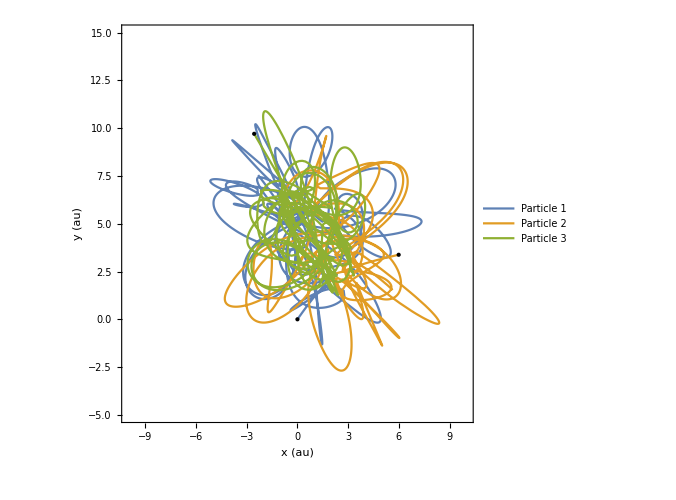

Seed: 121

Key length: 1920192

Counts: <|0→969291,1→950901|>

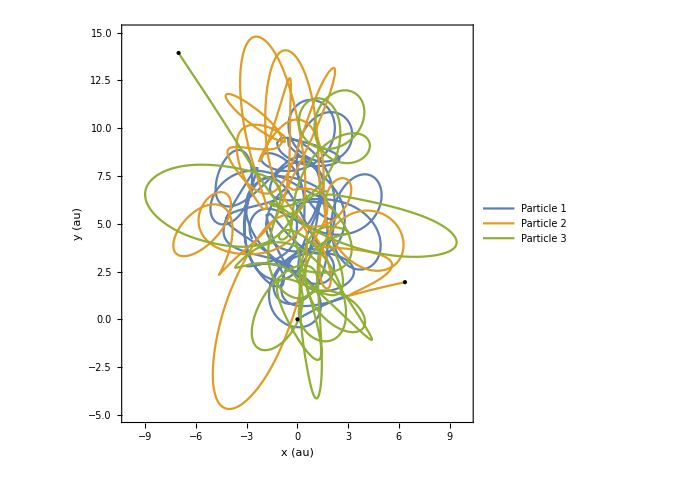

Seed 67 timing: 0.465435 seconds

Seed 12 timing: 0.440559 seconds

XOR key length: 1920192

XOR key counts: <|0→961442,1→958750|>

```mathematica
{time1,key1}=AbsoluteTiming[generateKeyWithPlot[105]];
{time2,key2}=AbsoluteTiming[generateKeyWithPlot[121]];

len=Min[Length[key1],Length[key2]];
key=BitXor[key1[[;;len]],key2[[;;len]]];

Print["Seed 67 timing: ",time1," seconds"];
Print["Seed 12 timing: ",time2," seconds"];
Print["XOR key length: ",len];
Print["XOR key counts: ",Counts[key]];
```

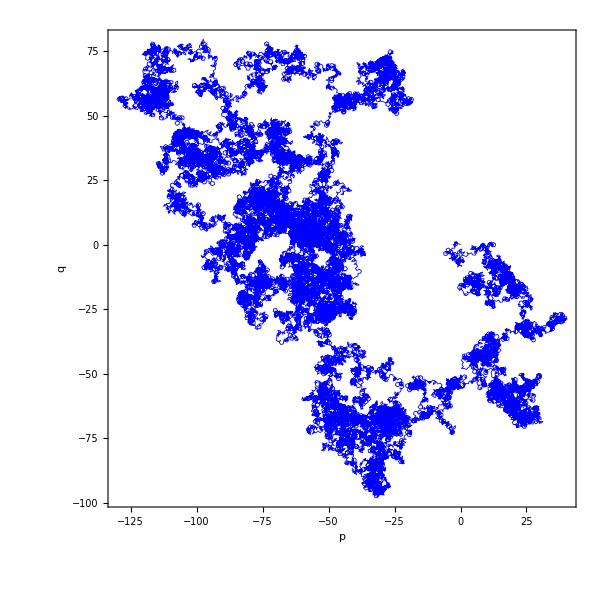

```mathematica
len=100000;
x=Take[key,len];   (*only first 1000 elements from key*)

c=1.2;   (*fixed constant for reproducibility*)

p=Accumulate[Table[x[[j]] Cos[j c],{j,1,len}]];
q=Accumulate[Table[x[[j]] Sin[j c],{j,1,len}]];


ListLinePlot[Transpose[{p,q}],PlotStyle->{Blue,Thickness[0.001]},AspectRatio->1,Axes->False,GridLines->None,Frame->True,FrameStyle->Directive[Black,Thickness[0.002],FontSize->12],FrameLabel->{Style["p",Italic,FontSize->14],Style["q",Italic,FontSize->14]},ImageSize->600,PlotRange->{{Min[p],Max[p]},{Min[q],Max[q]}},PlotRangePadding->Scaled[0.05] ]
```

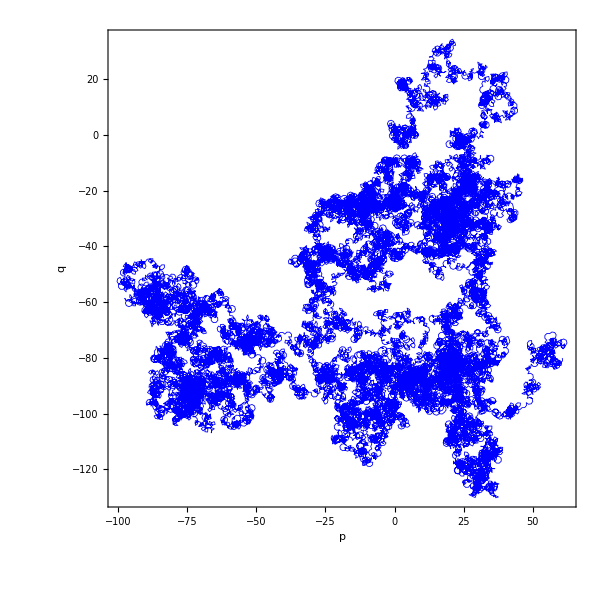

```mathematica
len=100000;
x=Take[key,len];   (*only first 1000 elements from key*)

c=0.8;   (*fixed constant for reproducibility*)

p=Accumulate[Table[x[[j]] Cos[j c],{j,1,len}]];
q=Accumulate[Table[x[[j]] Sin[j c],{j,1,len}]];



ListLinePlot[Transpose[{p,q}],PlotStyle->{Blue,Thickness[0.001]},AspectRatio->1,Axes->False,GridLines->None,Frame->True,FrameStyle->Directive[Black,Thickness[0.002],FontSize->12],FrameLabel->{Style["p",Italic,FontSize->14],Style["q",Italic,FontSize->14]},ImageSize->600,PlotRange->{{Min[p],Max[p]},{Min[q],Max[q]}},PlotRangePadding->Scaled[0.05] ]
```

```mathematica
bitString=StringJoin[ToString/@key];
Export["input00",bitString,"Text"]
```

input00

```mathematica
(*SerialRandomnessTest*)
serialResult=N@ResourceFunction["SerialRandomnessTest"][key,"TestStatistic"];
serialPValue=N@ResourceFunction["SerialRandomnessTest"][key,"PValue"];
Print["Serial Randomness Test:"];
Print["  Test Statistic: ",serialResult];
Print["  P-Value: ",serialPValue];
If[serialPValue>0.05,Print["  Result: Good randomness (p-value > 0.05)"],Print["  Result: Bad randomness (p-value ≤ 0.05)"]];

(*ChiSquareRandomnessTest*)
chiSquareResult=N@ResourceFunction["ChiSquareRandomnessTest"][key,"TestStatistic"];
chiSquarePValue=N@ResourceFunction["ChiSquareRandomnessTest"][key,"PValue"];
Print["\nChi-Square Randomness Test:"];
Print["  Test Statistic: ",chiSquareResult];
Print["  P-Value: ",chiSquarePValue];
If[chiSquarePValue>0.05,Print["  Result: Good randomness (p-value > 0.05)"],Print["  Result: Bad randomness (p-value ≤ 0.05)"]];

(*BinaryRunRandomnessTest*)
binaryRunResult=N@ResourceFunction["BinaryRunRandomnessTest"][key,"TestStatistic"];
binaryRunPValue=N@ResourceFunction["BinaryRunRandomnessTest"][key,"PValue"];
Print["\nBinary Run Randomness Test:"];
Print["  Test Statistic: ",binaryRunResult];
Print["  P-Value: ",binaryRunPValue];
If[binaryRunPValue>0.05,Print["  Result: Good randomness (p-value > 0.05)"],Print["  Result: Bad randomness (p-value ≤ 0.05)"]];

(*ArcsineLawRandomnessTest*)
arcsineResult=N@ResourceFunction["ArcsineLawRandomnessTest"][key,"TestStatistic"];
arcsinePValue=N@ResourceFunction["ArcsineLawRandomnessTest"][key,"PValue"]; (*Force numeric evaluation*)
Print["\nArcsine Law Randomness Test:"];
Print["  Test Statistic: ",arcsineResult];
Print["  P-Value: ",arcsinePValue];
If[arcsinePValue>0.05,Print["  Result: Good randomness (p-value > 0.05)"],Print["  Result: Bad randomness (p-value ≤ 0.05)"]];
```

Serial Randomness Test:

Test Statistic: 0.841303

P-Value: 0.643647

Result: Good randomness (p-value > 0.05)

Chi-Square Randomness Test:

Test Statistic: 0.44758

P-Value: 0.503486

Result: Good randomness (p-value > 0.05)

Binary Run Randomness Test:

Test Statistic: 71950.

P-Value: 0.521199

Result: Good randomness (p-value > 0.05)

Arcsine Law Randomness Test:

Test Statistic: 0.414259

P-Value: 0.890289

Serial Randomness Test:

Test Statistic: 2.04372

P-Value: 0.317225

Result: Good randomness (p-value > 0.05)

Chi-Square Randomness Test:

Test Statistic: 2.56455

P-Value: 0.109284

Result: Good randomness (p-value > 0.05)

Binary Run Randomness Test:

Test Statistic: 72099.

P-Value: 0.881562

Result: Good randomness (p-value > 0.05)

Arcsine Law Randomness Test:

Test Statistic: 0.884928

P-Value: 0.440657

Result: Good randomness (p-value > 0.05)

Serial Randomness Test:

Test Statistic: 2.04372

P-Value: 0.317225

Result: Good randomness (p-value > 0.05)

Chi-Square Randomness Test:

Test Statistic: 2.56455

P-Value: 0.109284

Result: Good randomness (p-value > 0.05)

Binary Run Randomness Test:

Test Statistic: 72099.

P-Value: 0.881562

Result: Good randomness (p-value > 0.05)

Arcsine Law Randomness Test:

Test Statistic: 0.884928

P-Value: 0.440657

Result: Good randomness (p-value > 0.05)

Serial Randomness Test:

Test Statistic: 2.04372

P-Value: 0.317225

Result: Good randomness (p-value > 0.05)

Chi-Square Randomness Test:

Test Statistic: 2.56455

P-Value: 0.109284

Result: Good randomness (p-value > 0.05)

Binary Run Randomness Test:

Test Statistic: 72099.

P-Value: 0.881562

Result: Good randomness (p-value > 0.05)

Arcsine Law Randomness Test:

Test Statistic: 0.884928

P-Value: 0.440657

Result: Good randomness (p-value > 0.05)

Serial Randomness Test:

Test Statistic: 4.9488

P-Value: 0.0535168

Result: Good randomness (p-value > 0.05)

Chi-Square Randomness Test:

Test Statistic: 0.0575942

P-Value: 0.81034

Result: Good randomness (p-value > 0.05)

Binary Run Randomness Test:

Test Statistic: 719947.

P-Value: 0.835014

Result: Good randomness (p-value > 0.05)

Arcsine Law Randomness Test:

Test Statistic: 0.781273

P-Value: 0.619643

Result: Good randomness (p-value > 0.05)

Serial Randomness Test:

Test Statistic: 2.93474

P-Value: 0.184944

Result: Good randomness (p-value > 0.05)

Chi-Square Randomness Test:

Test Statistic: 0.541821

P-Value: 0.461679

Result: Good randomness (p-value > 0.05)

Binary Run Randomness Test:

Test Statistic: 240329.

P-Value: 0.378211

Result: Good randomness (p-value > 0.05)

Arcsine Law Randomness Test:

Test Statistic: 0.891009

P-Value: 0.428381

Result: Good randomness (p-value > 0.05)

Result: Good randomness (p-value > 0.05)

```mathematica
GenerateSBoxesFromStream[bitstream_List,boxLength_Integer,count_Integer:3]:=Module[{bitsPerEntry,totalBits,chunks,makeSBox,sboxes},(*Bits needed per entry (e.g.5 bits for 32-entry S-box)*)bitsPerEntry=Ceiling[Log2[boxLength]];
totalBits=boxLength*bitsPerEntry;
If[Length[bitstream]<count*totalBits,Return[$Failed,Module]];
(*Helper:convert bit chunk to S-box*)makeSBox[bits_]:=Module[{partitioned,decimals,unique},partitioned=Partition[bits,bitsPerEntry];
decimals=FromDigits[#,2]&/@partitioned;
unique=DeleteDuplicates[decimals];
If[Length[unique]==boxLength,unique,Join[unique,Complement[Range[0,boxLength-1],unique]]]];
(*Slice stream into chunks and generate S-boxes*)chunks=Partition[bitstream,totalBits][[;;count]];
sboxes=makeSBox/@chunks;
sboxes]
```

```mathematica
EvalSbox[sbox_]:=(
sboxBitCount = Log[2,Length[sbox]];
sboxBitsLists = Table[IntegerDigits[sbox[[i]],2,sboxBitCount],{i,Length[sbox]}];
sboxBitLvlsList = Table[Table[sboxBitsLists[[i]][[j]],{i,Length[sbox]}],{j,sboxBitCount}];

NaturalBasis[s_]:=With[{u={{1,1},{1,-1}}},Nest[ArrayFlatten[#/.{1->u,-1->-u}]&,{{1}},s]];
walshM = NaturalBasis[sboxBitCount];
nonLin = 0;
For[i=1,i<=Length[sboxBitLvlsList],i++,nonLin=Max[nonLin,2^(sboxBitCount-1)-Max[Abs[Drop[sboxBitLvlsList[[i]].walshM,1]]]]];
nonLin = TextString[nonLin];
(*Print[StringJoin["Nonlinearity = ",nonLin]];*)


SACRes2D = Table[Table[0,{i,sboxBitCount}],{j,sboxBitCount}];
calBitVal[m_,n_,testVal_]:=BitAnd[IntegerPart[testVal/(2^n)],1];
For[m=0,m<sboxBitCount,m++,For[i=0,i≤Length[sbox]-1,i++,For[n=0,n<sboxBitCount,n++,SACRes2D[[m+1]][[n+1]]+=calBitVal[m,n,BitXor[sbox[[i+1]],sbox[[BitXor[i,2^m]+1]]]]]]];

SAC = TextString[Total[Total[SACRes2D/(2^sboxBitCount)]]/sboxBitCount^2];
(*Print[StringJoin["SAC = ", SAC];*)

BIC = TextString[2^(sboxBitCount-1)-Max[Abs[2^(sboxBitCount-1)-Flatten[SACRes2D]]]];
(*Print[StringJoin["BIC = ", BIC]];*)

LAP = TextString[Max[Abs[(Flatten[SACRes2D]/2^(sboxBitCount))-0.5]]];
(*Print[StringJoin["LAP = ", LAP]];*)


DifList2D = Table[0,{i,(2^sboxBitCount)}];
For[i=1,i<=Length[sbox],i++,For[j=1,j<=Length[sbox],j++,DifList2D[[i]]+=((sbox[[i]]-sbox[[j]]))]];

DAP = TextString[1/Mean[Abs[DifList2D/2^(sboxBitCount)]]];
(*Print[StringJoin["DAP = ", DAP]];*)
Return[{"nonLin" ->nonLin, "SAC" -> SAC, "BIC"->BIC, "LAP"-> LAP, "DAP"-> DAP}];

)


(*Test on ASCON S-box*)
ASCONsbox={4,11,31,20,26,21,9,2,27,5,8,18,29,3,6,28,30,19,7,14,0,13,17,24,16,12,1,25,22,10,15,23};
result=EvalSbox[ASCONsbox];
Print["\nResult: ",result];
```

Result: {nonLin→8,SAC→0.62,BIC→0,LAP→0.5,DAP→0.125}

```mathematica
EvalSbox2[sbox_]:=(sboxBitCount=Log[2,Length[sbox]];
sboxBitsLists=Table[IntegerDigits[sbox[[i]],2,sboxBitCount],{i,Length[sbox]}];
sboxBitLvlsList=Table[Table[sboxBitsLists[[i]][[j]],{i,Length[sbox]}],{j,sboxBitCount}];
NaturalBasis[s_]:=With[{u={{1,1},{1,-1}}},Nest[ArrayFlatten[#/. {1->u,-1->-u}]&,{{1}},s]];
walshM=NaturalBasis[sboxBitCount];
nonLin=0;
For[i=1,i<=Length[sboxBitLvlsList],i++,nonLin=Max[nonLin,2^(sboxBitCount-1)-Max[Abs[Drop[sboxBitLvlsList[[i]].walshM,1]]]]];
nonLin=TextString[nonLin];
SACRes2D=Table[Table[0,{i,sboxBitCount}],{j,sboxBitCount}];
calBitVal[m_,n_,testVal_]:=BitAnd[IntegerPart[testVal/(2^n)],1];
For[m=0,m<sboxBitCount,m++,For[i=0,i<=Length[sbox]-1,i++,For[n=0,n<sboxBitCount,n++,SACRes2D[[m+1]][[n+1]]+=calBitVal[m,n,BitXor[sbox[[i+1]],sbox[[BitXor[i,2^m]+1]]]]]]];
SAC=TextString[Total[Total[SACRes2D/(2^sboxBitCount)]]/sboxBitCount^2];


(*---FIXED:Differential Approximation Probability (DAP)---*)DAP=0;
For[a=1,a<2^sboxBitCount,a++,For[b=0,b<2^sboxBitCount,b++,count=Count[Table[BitXor[sbox[[x+1]],sbox[[BitXor[x,a]+1]]],{x,0,2^sboxBitCount-1}],b];
DAP=Max[DAP,count/2^sboxBitCount];]];
DAP=TextString[DAP];


(*---Corrected Linear Approximation Probability (LAP)---*)LAP=0;
For[a=1,a<2^sboxBitCount,a++,For[b=0,b<2^sboxBitCount,b++,parity=Table[(-1)^(BitAnd[BitXor[Dot[IntegerDigits[a,2,sboxBitCount],IntegerDigits[x,2,sboxBitCount]],Dot[IntegerDigits[b,2,sboxBitCount],IntegerDigits[sbox[[x+1]],2,sboxBitCount]]],1]),{x,0,2^sboxBitCount-1}];
val=Abs[Total[parity]]/(2^sboxBitCount);
LAP=Max[LAP,val/2];  (*normalize to probability space*)]];
LAP=TextString[LAP];

(*---Corrected Bit Independence Criterion (BIC)---*)
bitCorr={};
For[i=1,i<=sboxBitCount,i++,For[j=i+1,j<=sboxBitCount,j++,AppendTo[bitCorr,Abs[Correlation[sboxBitLvlsList[[i]],sboxBitLvlsList[[j]]]]];]];
BIC=TextString[Mean[bitCorr]];


Return[{"nonLin"->nonLin,"SAC"->SAC,"BIC"->BIC,"LAP"->LAP,"DAP"->DAP}])


ASCONsbox={4,11,31,20,26,21,9,2,27,5,8,18,29,3,6,28,30,19,7,14,0,13,17,24,16,12,1,25,22,10,15,23};
result=EvalSbox2[ASCONsbox];
Print["\nResult (new Eval function): ",result];
```

Result (new Eval function): {nonLin→8,SAC→0.62,BIC→0,LAP→0.25,DAP→0.25}

```mathematica
Print["S-box Metric Guidance (definitions & desirable directions):"];
Print["  nonLin -> Higher is better (resists linear attacks)."];
Print["             Theoretical max nonLinearity = 12."];
Print["  SAC    -> Ideal = 0.5 (avalanche). Values near 0.5 are desirable."];
Print["  BIC    -> (mean |corr| between output bits) : Lower is better (0 = perfect independence)."];

Print["  LAP    -> Lower is better. (LAP = max |LAT| / 2^n, normalized; smaller bias is better)."];
Print["  DAP    -> Lower is better. (DAP = max entry of the DDT / 2^n, probability; smaller is better)."];
```

S-box Metric Guidance (definitions & desirable directions):

nonLin -> Higher is better (resists linear attacks).

Theoretical max nonLinearity = 12.

SAC    -> Ideal = 0.5 (avalanche). Values near 0.5 are desirable.

BIC    -> (mean |corr| between output bits) : Lower is better (0 = perfect independence).

LAP    -> Lower is better. (LAP = max |LAT| / 2^n, normalized; smaller bias is better).

DAP    -> Lower is better. (DAP = max entry of the DDT / 2^n, probability; smaller is better).

```mathematica
(*1) Generate S-boxes*)asconSBoxes=GenerateSBoxesFromStream[key,32,1000];

(*2) Evaluate each S-box*)
rawEvals=EvalSbox2/@asconSBoxes;

(*3) Normalize:convert list of rules with string values->Association with numeric values*)
normalizeEval[eval_]:=Association@KeyValueMap[Function[{k,v},ToString[k]->Quiet@Check[ToExpression[v],v]],Association[eval]];

numericEvals=normalizeEval/@rawEvals;

(*4) Pair S-box with its evaluation*)
paired=MapThread[<|"SBox"->#1,"Eval"->#2|>&,{asconSBoxes,numericEvals}];

(*5) Filter by multiple conditions*)
good=Select[paired,Function[p,Module[{e=p["Eval"]},
e["nonLin"]>8&&
e["SAC"]>=0.45&&e["SAC"]<=0.55&&
e["BIC"]>=0.0&&e["BIC"]<=0.5&&
e["LAP"]<=0.25&&e["DAP"]<=0.25 ]]];

(*6) Output results*)
Print["Strong S-boxes found: ",Length[good]];

Do[Print["S-box ",i,": ",good[[i,"SBox"]],"  nonLin = ",good[[i,"Eval","nonLin"]],"  SAC = ",good[[i,"Eval","SAC"]],"  BIC = ",good[[i,"Eval","BIC"]],"  LAP = ",good[[i,"Eval","LAP"]],"  DAP = ",good[[i,"Eval","DAP"]]],{i,Length[good]}];
```

Strong S-boxes found: 262

S-box 1: {0,5,31,14,7,8,1,22,11,16,2,12,10,29,20,4,17,9,25,3,6,13,15,18,19,21,23,24,26,27,28,30}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 2: {21,1,17,13,6,5,22,26,8,0,23,20,12,9,3,10,2,14,15,25,30,4,7,11,16,18,19,24,27,28,29,31}  nonLin = 10  SAC = 0.49  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 3: {31,24,15,10,16,20,6,27,7,21,29,11,30,23,28,26,13,25,5,0,1,2,3,4,8,9,12,14,17,18,19,22}  nonLin = 10  SAC = 0.45  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 4: {10,22,16,25,18,28,14,4,19,13,15,6,26,2,7,21,0,1,20,12,3,5,8,9,11,17,23,24,27,29,30,31}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 5: {8,15,5,29,1,9,26,21,22,13,14,20,17,16,3,6,2,30,31,12,10,0,4,7,11,18,19,23,24,25,27,28}  nonLin = 10  SAC = 0.53  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 6: {6,22,25,28,17,29,30,31,1,8,16,3,12,24,10,26,7,19,23,11,13,0,2,4,5,9,14,15,18,20,21,27}  nonLin = 10  SAC = 0.53  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 7: {24,27,3,21,29,12,17,2,7,26,8,20,13,4,28,9,19,15,11,14,0,1,5,6,10,16,18,22,23,25,30,31}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 8: {21,23,8,7,24,30,26,31,14,5,27,16,28,22,20,6,18,12,0,3,1,2,4,9,10,11,13,15,17,19,25,29}  nonLin = 10  SAC = 0.485  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 9: {11,1,14,10,31,23,5,0,24,22,29,17,21,6,15,27,8,19,26,9,2,3,4,7,12,13,16,18,20,25,28,30}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 10: {21,14,10,28,7,9,12,5,3,25,1,8,20,0,2,16,26,19,24,4,31,27,6,11,13,15,17,18,22,23,29,30}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 11: {30,9,1,12,20,0,2,24,4,8,22,25,27,13,15,16,11,21,19,26,7,3,5,6,10,14,17,18,23,28,29,31}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 12: {8,11,13,5,19,28,31,3,25,29,15,12,30,14,20,17,16,0,10,24,1,2,4,6,7,9,18,21,22,23,26,27}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 13: {0,3,19,27,4,22,24,23,16,12,9,5,28,26,20,25,30,17,10,1,2,6,7,8,11,13,14,15,18,21,29,31}  nonLin = 10  SAC = 0.505  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 14: {23,24,20,31,22,21,28,7,1,15,30,25,16,5,2,9,4,19,3,26,0,6,8,10,11,12,13,14,17,18,27,29}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 15: {29,5,4,28,24,27,2,11,13,1,21,15,26,31,7,10,16,0,3,6,8,9,12,14,17,18,19,20,22,23,25,30}  nonLin = 10  SAC = 0.46  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 16: {21,25,22,4,19,28,8,26,7,3,9,18,13,15,17,20,24,30,5,0,1,2,6,10,11,12,14,16,23,27,29,31}  nonLin = 10  SAC = 0.53  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 17: {1,25,4,14,31,17,0,20,15,24,11,10,19,7,26,9,22,16,2,3,5,6,8,12,13,18,21,23,27,28,29,30}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 18: {12,22,31,15,18,20,13,26,17,0,24,9,3,25,4,5,21,8,1,27,2,6,7,10,11,14,16,19,23,28,29,30}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 19: {8,0,5,14,3,26,22,2,11,16,28,9,1,12,6,31,21,23,7,30,4,10,13,15,17,18,19,20,24,25,27,29}  nonLin = 10  SAC = 0.49  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 20: {17,28,9,25,11,30,3,7,12,10,0,29,16,27,13,23,15,8,19,21,1,2,4,5,6,14,18,20,22,24,26,31}  nonLin = 10  SAC = 0.48  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 21: {30,16,22,1,18,31,3,7,5,27,25,9,0,29,12,17,13,14,2,24,28,4,6,8,10,11,15,19,20,21,23,26}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 22: {0,31,10,18,23,17,7,16,13,3,12,27,4,29,21,11,8,26,30,19,1,2,5,6,9,14,15,20,22,24,25,28}  nonLin = 10  SAC = 0.505  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 23: {12,4,26,27,10,31,0,13,19,21,30,3,15,6,2,1,17,18,8,20,28,5,7,9,11,14,16,22,23,24,25,29}  nonLin = 10  SAC = 0.55  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 24: {30,0,9,3,10,31,13,8,12,11,2,16,21,7,25,14,23,4,5,1,6,15,17,18,19,20,22,24,26,27,28,29}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 25: {29,1,14,28,4,0,15,8,13,18,23,26,10,25,12,2,7,16,24,17,9,3,5,6,11,19,20,21,22,27,30,31}  nonLin = 10  SAC = 0.505  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 26: {25,27,30,2,13,28,23,5,16,3,29,31,17,24,14,21,12,1,0,4,6,7,8,9,10,11,15,18,19,20,22,26}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 27: {10,15,28,17,27,12,1,25,11,31,4,5,14,16,3,7,19,8,13,0,2,6,9,18,20,21,22,23,24,26,29,30}  nonLin = 10  SAC = 0.5  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 28: {10,15,28,14,2,16,6,18,26,12,24,3,7,21,19,11,5,4,27,31,9,1,0,8,13,17,20,22,23,25,29,30}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 29: {9,22,8,0,5,15,19,11,26,25,16,13,27,7,6,2,3,4,30,10,1,12,14,17,18,20,21,23,24,28,29,31}  nonLin = 10  SAC = 0.5  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 30: {22,8,12,6,23,30,21,28,16,9,3,15,11,17,10,4,26,5,31,1,0,2,7,13,14,18,19,20,24,25,27,29}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 31: {5,12,28,22,31,26,1,27,21,8,23,3,14,18,16,30,15,19,4,17,11,0,2,6,7,9,10,13,20,24,25,29}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 32: {0,28,14,8,16,5,3,30,6,20,23,9,10,1,18,31,27,21,26,22,2,4,7,11,12,13,15,17,19,24,25,29}  nonLin = 12  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 33: {23,24,25,5,31,10,28,8,19,1,13,3,15,17,22,27,4,16,6,20,0,2,7,9,11,12,14,18,21,26,29,30}  nonLin = 10  SAC = 0.5  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 34: {13,27,0,14,29,1,7,5,10,19,8,4,30,15,24,2,25,28,16,3,6,9,11,12,17,18,20,21,22,23,26,31}  nonLin = 10  SAC = 0.49  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 35: {31,25,21,16,5,23,9,7,28,11,1,26,4,30,2,6,29,0,3,8,10,12,13,14,15,17,18,19,20,22,24,27}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 36: {7,9,21,31,10,24,29,25,11,13,26,14,17,27,6,23,28,3,16,4,30,8,0,1,2,5,12,15,18,19,20,22}  nonLin = 10  SAC = 0.475  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 37: {8,2,9,21,26,1,0,24,20,19,5,23,18,12,10,30,14,16,3,4,6,7,11,13,15,17,22,25,27,28,29,31}  nonLin = 10  SAC = 0.49  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 38: {7,12,29,15,23,2,16,8,22,24,0,6,5,1,31,18,19,10,3,21,28,9,4,11,13,14,17,20,25,26,27,30}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 39: {19,23,1,27,16,24,22,15,13,9,17,10,3,8,26,28,2,31,18,20,25,0,4,5,6,7,11,12,14,21,29,30}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 40: {1,2,7,6,26,3,21,24,22,15,5,20,23,10,0,11,9,29,4,17,14,27,12,31,8,13,16,18,19,25,28,30}  nonLin = 12  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 41: {14,30,25,19,17,28,5,3,26,21,2,11,7,24,29,15,0,8,18,1,4,6,9,10,12,13,16,20,22,23,27,31}  nonLin = 10  SAC = 0.505  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 42: {27,7,23,25,0,6,30,15,22,20,17,12,3,5,4,9,2,24,13,11,1,14,28,8,10,16,18,19,21,26,29,31}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 43: {27,20,14,13,28,26,30,3,12,31,17,5,6,10,9,2,21,24,23,0,1,4,7,8,11,15,16,18,19,22,25,29}  nonLin = 10  SAC = 0.53  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 44: {2,29,31,19,3,6,1,15,10,18,27,8,25,12,7,9,17,11,28,0,4,5,13,14,16,20,21,22,23,24,26,30}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 45: {17,9,11,21,26,14,7,19,1,28,10,24,25,2,12,30,15,20,22,31,0,3,4,5,6,8,13,16,18,23,27,29}  nonLin = 10  SAC = 0.545  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 46: {24,2,19,29,21,13,15,3,6,0,8,10,12,11,22,4,7,5,14,17,31,1,9,16,18,20,23,25,26,27,28,30}  nonLin = 10  SAC = 0.535  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 47: {28,5,7,25,14,16,26,19,24,1,2,12,22,3,11,10,31,8,17,27,0,4,6,9,13,15,18,20,21,23,29,30}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 48: {21,24,20,5,27,16,1,28,12,30,6,4,31,9,15,25,7,3,17,10,18,2,23,0,8,11,13,14,19,22,26,29}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 49: {20,22,7,28,26,8,24,30,19,1,9,0,2,25,18,6,5,15,16,31,27,3,4,10,11,12,13,14,17,21,23,29}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 50: {21,22,18,3,15,26,27,17,11,2,16,9,28,4,1,25,24,13,14,0,5,6,7,8,10,12,19,20,23,29,30,31}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 51: {4,28,25,11,23,13,27,16,6,21,20,2,14,24,3,0,10,7,31,29,5,22,1,8,9,12,15,17,18,19,26,30}  nonLin = 10  SAC = 0.55  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 52: {31,10,7,26,25,11,20,2,30,4,9,3,29,12,6,15,16,0,28,5,21,27,1,8,13,14,17,18,19,22,23,24}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 53: {8,1,9,19,7,30,0,15,16,2,26,24,31,17,14,4,28,21,20,22,11,3,5,6,10,12,13,18,23,25,27,29}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 54: {1,12,19,10,25,5,30,20,14,0,16,2,13,17,31,18,15,21,6,7,22,3,4,8,9,11,23,24,26,27,28,29}  nonLin = 10  SAC = 0.505  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 55: {29,21,14,22,25,16,0,12,24,28,26,10,23,9,18,3,11,19,20,1,2,4,5,6,7,8,13,15,17,27,30,31}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 56: {20,8,16,22,5,18,24,11,27,7,4,23,30,13,28,12,10,0,15,14,29,1,2,3,6,9,17,19,21,25,26,31}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 57: {22,6,17,20,9,3,30,14,11,28,25,10,23,19,24,21,26,0,5,1,2,4,7,8,12,13,15,16,18,27,29,31}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 58: {24,2,11,1,7,0,25,14,19,4,10,31,15,8,21,30,22,12,18,13,23,3,5,6,9,16,17,20,26,27,28,29}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 59: {13,0,16,25,11,8,12,21,15,31,28,2,6,27,19,18,29,23,20,7,24,14,1,3,4,5,9,10,17,22,26,30}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 60: {20,9,14,27,4,30,29,15,3,19,10,25,8,18,7,28,21,6,23,2,11,0,1,5,12,13,16,17,22,24,26,31}  nonLin = 10  SAC = 0.53  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 61: {10,20,11,6,29,1,18,22,5,24,14,0,15,2,27,12,26,21,28,23,17,3,4,7,8,9,13,16,19,25,30,31}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 62: {6,27,19,23,5,21,8,22,9,29,20,3,11,16,12,14,30,24,31,7,4,0,1,2,10,13,15,17,18,25,26,28}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 63: {15,18,16,23,25,10,11,8,0,17,29,19,2,14,22,21,28,3,7,31,1,4,5,6,9,12,13,20,24,26,27,30}  nonLin = 10  SAC = 0.53  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 64: {18,1,4,21,22,5,6,11,0,31,29,14,2,26,20,3,7,8,9,10,12,13,15,16,17,19,23,24,25,27,28,30}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 65: {3,0,5,10,26,8,20,24,11,16,15,25,22,29,18,7,21,12,28,6,9,1,2,4,13,14,17,19,23,27,30,31}  nonLin = 10  SAC = 0.5  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 66: {24,6,3,16,27,30,22,12,18,15,23,11,0,4,20,2,7,17,28,21,1,5,8,9,10,13,14,19,25,26,29,31}  nonLin = 12  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 67: {4,9,13,27,25,3,19,15,7,23,6,21,11,30,18,29,12,28,22,0,1,2,5,8,10,14,16,17,20,24,26,31}  nonLin = 10  SAC = 0.505  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 68: {20,28,10,30,31,18,17,9,0,13,25,24,22,11,26,2,3,4,7,6,27,16,8,15,1,5,12,14,19,21,23,29}  nonLin = 10  SAC = 0.485  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 69: {18,2,31,15,16,19,1,10,13,5,14,30,6,28,22,17,11,24,0,3,4,7,8,9,12,20,21,23,25,26,27,29}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 70: {20,13,23,3,2,22,12,28,21,4,30,27,1,17,26,24,10,7,5,29,11,0,6,8,9,14,15,16,18,19,25,31}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 71: {22,11,27,2,14,25,29,1,3,18,24,23,7,13,26,19,10,12,5,0,4,6,8,9,15,16,17,20,21,28,30,31}  nonLin = 10  SAC = 0.5  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 72: {5,15,27,3,14,19,21,8,2,24,17,1,7,11,31,12,16,4,23,0,6,9,10,13,18,20,22,25,26,28,29,30}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 73: {27,20,2,18,11,7,15,12,31,21,26,4,24,10,0,29,23,28,1,3,5,6,8,9,13,14,16,17,19,22,25,30}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 74: {8,4,25,28,15,9,31,10,11,12,18,22,19,29,7,14,0,23,1,2,3,5,6,13,16,17,20,21,24,26,27,30}  nonLin = 10  SAC = 0.475  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 75: {10,13,22,27,14,0,21,8,24,12,2,15,7,3,31,9,26,18,29,19,5,16,6,1,4,11,17,20,23,25,28,30}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 76: {29,9,22,8,0,3,4,15,11,5,23,14,21,27,1,20,7,17,2,6,10,12,13,16,18,19,24,25,26,28,30,31}  nonLin = 10  SAC = 0.54  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 77: {13,12,21,0,24,17,15,23,3,27,8,18,7,31,20,4,6,25,1,2,5,9,10,11,14,16,19,22,26,28,29,30}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 78: {14,30,10,28,12,25,22,23,1,29,13,19,24,9,16,0,31,6,21,2,3,4,5,7,8,11,15,17,18,20,26,27}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 79: {24,23,30,28,7,5,31,14,17,26,16,13,15,27,21,8,22,2,1,0,3,4,6,9,10,11,12,18,19,20,25,29}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 80: {27,31,7,13,19,0,22,17,26,8,2,28,18,30,23,3,11,16,5,9,24,1,4,6,10,12,14,15,20,21,25,29}  nonLin = 10  SAC = 0.48  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 81: {0,2,23,5,8,25,21,10,24,26,7,17,22,4,16,30,31,28,15,1,3,6,9,11,12,13,14,18,19,20,27,29}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 82: {11,5,4,31,12,30,25,21,9,15,23,10,19,27,0,8,22,3,2,1,24,6,7,13,14,16,17,18,20,26,28,29}  nonLin = 10  SAC = 0.545  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 83: {20,18,23,12,10,15,28,13,31,5,6,22,8,26,29,14,21,27,4,16,1,25,0,2,3,7,9,11,17,19,24,30}  nonLin = 10  SAC = 0.49  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 84: {21,14,1,15,31,12,16,10,20,11,26,9,2,7,28,18,0,23,4,17,27,3,5,6,8,13,19,22,24,25,29,30}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 85: {12,21,17,9,14,18,25,26,30,8,0,16,6,3,15,23,19,2,29,10,27,1,4,5,7,11,13,20,22,24,28,31}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 86: {3,10,4,15,20,22,31,16,0,5,17,2,1,19,29,30,13,8,12,28,7,26,6,9,11,14,18,21,23,24,25,27}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 87: {31,25,18,17,15,2,3,29,19,8,4,20,1,16,12,27,23,5,14,7,11,28,0,6,9,10,13,21,22,24,26,30}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 88: {11,8,3,28,29,20,15,17,27,26,12,7,23,14,9,24,18,13,0,1,2,4,5,6,10,16,19,21,22,25,30,31}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 89: {25,15,29,24,7,23,0,26,2,17,21,16,13,28,19,30,9,31,20,1,3,4,5,6,8,10,11,12,14,18,22,27}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 90: {26,17,20,15,24,1,23,31,4,10,7,18,13,5,19,28,22,27,9,25,14,0,29,2,3,6,8,11,12,16,21,30}  nonLin = 10  SAC = 0.53  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 91: {22,11,2,1,31,14,9,6,27,24,16,18,20,13,28,0,12,4,8,19,23,21,3,5,7,10,15,17,25,26,29,30}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 92: {14,18,8,0,15,11,28,16,13,19,22,26,25,17,4,7,1,10,9,24,30,2,3,5,6,12,20,21,23,27,29,31}  nonLin = 10  SAC = 0.505  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 93: {2,24,0,5,6,8,26,18,1,30,12,16,28,15,17,31,3,11,23,7,10,19,4,13,9,14,20,21,22,25,27,29}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 94: {14,18,28,13,27,29,10,12,9,23,22,8,11,16,17,26,24,31,0,19,4,30,1,2,3,5,6,7,15,20,21,25}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 95: {9,7,29,14,1,4,23,15,27,19,28,8,13,12,30,18,22,0,6,31,17,2,3,5,10,11,16,20,21,24,25,26}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 96: {22,28,8,9,6,20,3,25,30,5,19,13,24,23,21,10,27,31,17,7,1,0,2,4,11,12,14,15,16,18,26,29}  nonLin = 10  SAC = 0.505  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 97: {7,5,11,20,1,14,2,30,13,0,4,19,21,24,3,15,6,12,8,9,10,16,17,18,22,23,25,26,27,28,29,31}  nonLin = 10  SAC = 0.505  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 98: {31,17,8,1,27,30,23,19,3,13,18,7,22,4,9,16,5,21,2,25,0,6,10,11,12,14,15,20,24,26,28,29}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 99: {8,4,3,6,14,0,26,19,12,13,17,18,15,24,21,1,29,20,22,10,2,5,7,9,11,16,23,25,27,28,30,31}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 100: {4,27,24,31,1,20,7,15,3,8,2,11,13,12,14,29,0,22,28,17,18,19,5,6,9,10,16,21,23,25,26,30}  nonLin = 10  SAC = 0.5  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 101: {4,23,28,0,7,5,17,13,14,6,19,1,31,21,26,3,16,12,15,11,2,8,9,10,18,20,22,24,25,27,29,30}  nonLin = 10  SAC = 0.48  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 102: {29,7,10,19,12,14,30,2,13,9,24,6,22,20,3,16,28,8,0,23,31,1,4,15,5,11,17,18,21,25,26,27}  nonLin = 10  SAC = 0.505  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 103: {28,4,13,16,25,15,20,9,5,23,12,10,6,7,21,11,0,14,19,27,26,1,2,3,8,17,18,22,24,29,30,31}  nonLin = 10  SAC = 0.49  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 104: {21,12,2,17,23,15,7,14,8,9,0,28,16,3,29,26,25,19,5,20,30,1,4,6,10,11,13,18,22,24,27,31}  nonLin = 10  SAC = 0.505  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 105: {0,31,18,4,14,2,20,3,6,1,11,19,22,15,17,29,7,9,26,24,5,8,10,12,13,16,21,23,25,27,28,30}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 106: {12,17,15,31,22,8,28,16,26,30,21,14,19,9,13,20,0,25,1,2,3,4,5,6,7,10,11,18,23,24,27,29}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 107: {23,26,10,6,28,18,4,11,7,30,8,29,17,31,14,12,3,22,24,27,0,16,2,25,1,5,9,13,15,19,20,21}  nonLin = 10  SAC = 0.49  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 108: {18,1,20,26,25,10,22,12,0,17,21,7,15,6,29,8,3,11,4,31,19,30,2,5,9,13,14,16,23,24,27,28}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 109: {31,26,18,19,25,28,13,5,6,2,29,0,20,22,27,9,11,12,10,17,1,3,4,7,8,14,15,16,21,23,24,30}  nonLin = 10  SAC = 0.49  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 110: {23,1,26,18,9,2,12,21,3,10,5,14,25,11,13,27,22,20,28,0,4,6,7,8,15,16,17,19,24,29,30,31}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 111: {18,29,0,12,11,1,6,17,5,20,10,24,31,23,28,4,14,21,13,22,2,3,7,8,9,15,16,19,25,26,27,30}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 112: {6,30,21,23,3,4,17,9,27,1,20,14,7,5,10,29,13,15,2,11,0,8,12,16,18,19,22,24,25,26,28,31}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 113: {25,10,3,15,28,1,17,20,12,19,0,18,29,30,31,23,16,4,9,8,2,5,6,7,11,13,14,21,22,24,26,27}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 114: {6,3,2,12,24,17,9,20,21,14,31,18,22,0,11,19,27,8,4,10,1,5,7,13,15,16,23,25,26,28,29,30}  nonLin = 10  SAC = 0.53  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 115: {14,31,3,21,28,10,23,5,4,9,13,30,19,24,8,0,1,2,6,7,11,12,15,16,17,18,20,22,25,26,27,29}  nonLin = 10  SAC = 0.505  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 116: {16,6,28,25,1,8,11,30,13,29,12,7,24,3,21,15,22,23,31,0,2,4,5,9,10,14,17,18,19,20,26,27}  nonLin = 10  SAC = 0.55  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 117: {15,24,10,30,26,17,14,19,21,22,20,7,16,12,28,9,29,2,3,18,0,1,4,5,6,8,11,13,23,25,27,31}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 118: {4,16,1,2,20,30,27,3,25,7,15,6,8,18,12,24,23,14,26,19,0,5,9,10,11,13,17,21,22,28,29,31}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 119: {7,23,31,4,6,17,25,0,19,2,15,16,11,29,10,3,24,9,18,28,26,12,22,1,5,8,13,14,20,21,27,30}  nonLin = 10  SAC = 0.535  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 120: {31,4,1,7,12,2,27,15,11,16,25,9,8,19,6,17,28,13,26,0,3,5,10,14,18,20,21,22,23,24,29,30}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 121: {30,20,3,14,0,25,7,29,2,4,17,21,18,8,16,13,23,31,1,24,5,9,6,10,11,12,15,19,22,26,27,28}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 122: {8,28,17,22,0,20,31,2,18,11,21,27,29,19,9,13,26,14,7,6,1,3,4,5,10,12,15,16,23,24,25,30}  nonLin = 12  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 123: {9,20,30,25,27,0,1,8,16,17,14,7,22,4,11,12,10,26,6,19,18,2,3,5,13,15,21,23,24,28,29,31}  nonLin = 10  SAC = 0.475  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 124: {13,23,1,18,12,29,9,19,2,10,4,27,8,26,21,24,22,0,3,5,6,7,11,14,15,16,17,20,25,28,30,31}  nonLin = 10  SAC = 0.5  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 125: {27,29,16,10,1,5,26,17,14,30,12,9,11,3,20,31,4,21,25,2,24,18,0,6,7,8,13,15,19,22,23,28}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 126: {7,27,20,0,16,2,11,24,4,31,28,30,25,15,5,6,14,26,10,3,13,1,8,9,12,17,18,19,21,22,23,29}  nonLin = 12  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 127: {7,17,3,27,21,1,18,28,23,25,14,22,9,19,16,0,8,20,24,15,2,4,5,6,10,11,12,13,26,29,30,31}  nonLin = 10  SAC = 0.5  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 128: {8,9,26,31,28,5,16,18,21,17,4,10,13,0,3,23,14,27,20,2,7,1,6,11,12,15,19,22,24,25,29,30}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 129: {20,26,2,8,1,4,13,16,3,27,30,31,28,0,14,24,19,12,5,11,29,6,7,9,10,15,17,18,21,22,23,25}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 130: {22,31,14,3,24,8,30,17,21,27,13,6,2,1,12,20,25,16,28,7,0,4,5,9,10,11,15,18,19,23,26,29}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 131: {16,26,14,20,6,13,24,4,15,10,31,22,8,19,21,18,9,12,27,23,5,3,25,0,1,2,7,11,17,28,29,30}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 132: {28,7,5,8,25,30,17,3,10,11,24,23,27,1,2,22,9,15,20,13,12,16,0,4,6,14,18,19,21,26,29,31}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 133: {4,17,31,19,26,15,18,28,9,29,21,6,8,0,12,10,20,16,5,11,1,2,3,7,13,14,22,23,24,25,27,30}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 134: {28,31,14,26,13,18,8,17,9,30,1,20,10,23,21,2,16,3,19,29,0,4,5,6,7,11,12,15,22,24,25,27}  nonLin = 10  SAC = 0.55  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 135: {26,7,2,22,25,28,11,3,17,18,15,19,5,21,16,6,8,0,10,1,4,9,12,13,14,20,23,24,27,29,30,31}  nonLin = 10  SAC = 0.505  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 136: {7,29,16,13,4,25,2,28,8,31,30,9,3,27,26,5,10,0,18,19,1,6,11,12,14,15,17,20,21,22,23,24}  nonLin = 10  SAC = 0.53  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 137: {3,12,13,16,20,1,30,8,23,7,22,2,9,6,25,10,4,18,0,5,11,14,15,17,19,21,24,26,27,28,29,31}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 138: {7,22,25,12,11,1,8,19,15,18,30,9,20,27,13,14,24,0,10,26,2,3,4,5,6,16,17,21,23,28,29,31}  nonLin = 10  SAC = 0.535  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 139: {18,0,22,25,5,6,26,13,24,10,12,3,19,15,4,31,14,7,1,2,8,9,11,16,17,20,21,23,27,28,29,30}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 140: {24,20,8,17,18,13,11,23,14,25,10,3,7,19,6,28,22,2,21,5,0,1,4,9,12,15,16,26,27,29,30,31}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 141: {13,15,4,26,8,16,19,24,29,22,7,27,21,6,31,14,2,3,9,0,1,5,10,11,12,17,18,20,23,25,28,30}  nonLin = 10  SAC = 0.505  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 142: {19,23,29,10,0,20,28,30,14,21,15,12,4,3,25,17,2,24,1,5,6,7,8,9,11,13,16,18,22,26,27,31}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 143: {4,21,24,29,13,27,10,11,18,6,1,26,16,31,20,17,14,3,2,22,0,5,7,8,9,12,15,19,23,25,28,30}  nonLin = 10  SAC = 0.55  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 144: {5,21,28,1,9,17,19,7,10,20,30,12,22,31,25,27,15,6,13,8,0,2,3,4,11,14,16,18,23,24,26,29}  nonLin = 10  SAC = 0.5  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 145: {18,31,6,23,9,11,4,13,16,12,14,24,22,25,28,2,17,3,21,10,0,1,5,7,8,15,19,20,26,27,29,30}  nonLin = 10  SAC = 0.49  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 146: {26,2,7,5,20,3,22,18,23,6,27,24,11,14,28,29,16,10,19,0,1,4,8,9,12,13,15,17,21,25,30,31}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 147: {16,23,1,28,25,7,30,21,27,15,24,18,14,12,22,26,20,29,5,0,2,3,4,6,8,9,10,11,13,17,19,31}  nonLin = 12  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 148: {23,20,19,13,24,9,17,12,21,14,27,18,29,22,10,3,16,28,31,2,26,7,0,1,4,5,6,8,11,15,25,30}  nonLin = 10  SAC = 0.545  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 149: {7,10,27,21,11,24,20,18,0,2,26,4,29,13,14,9,3,30,1,16,5,6,8,12,15,17,19,22,23,25,28,31}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 150: {9,5,17,20,24,22,4,0,1,25,26,14,16,12,3,23,31,28,2,19,18,6,7,8,10,11,13,15,21,27,29,30}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 151: {15,19,16,22,2,11,21,0,1,6,29,12,26,30,8,14,24,3,18,25,4,27,31,28,5,7,9,10,13,17,20,23}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 152: {10,22,3,18,5,14,25,0,26,6,9,23,21,27,30,15,24,28,31,7,17,11,29,1,2,4,8,12,13,16,19,20}  nonLin = 12  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 153: {25,30,28,6,27,15,13,29,17,4,31,11,23,3,22,5,8,20,7,21,0,1,2,9,10,12,14,16,18,19,24,26}  nonLin = 10  SAC = 0.48  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 154: {26,23,15,12,10,4,13,11,20,0,3,1,29,5,21,17,9,18,2,6,7,8,14,16,19,22,24,25,27,28,30,31}  nonLin = 10  SAC = 0.5  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 155: {3,11,24,27,5,14,25,20,9,29,18,26,30,21,23,22,6,13,7,17,8,28,0,1,2,4,10,12,15,16,19,31}  nonLin = 10  SAC = 0.49  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 156: {15,27,29,28,4,25,16,8,31,19,22,6,3,20,11,2,23,10,9,24,17,5,0,1,7,12,13,14,18,21,26,30}  nonLin = 10  SAC = 0.465  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 157: {17,0,10,2,23,28,29,7,18,20,14,12,13,9,3,5,19,6,11,26,1,4,8,15,16,21,22,24,25,27,30,31}  nonLin = 10  SAC = 0.465  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 158: {26,14,3,24,0,17,7,25,1,9,2,5,27,18,31,8,22,12,29,20,21,4,6,10,11,13,15,16,19,23,28,30}  nonLin = 10  SAC = 0.505  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 159: {25,17,8,4,24,11,21,31,5,20,10,30,14,22,12,29,28,9,27,7,13,2,0,1,3,6,15,16,18,19,23,26}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 160: {3,5,7,17,29,9,25,28,10,4,12,20,31,16,14,13,30,18,2,6,26,23,0,1,8,11,15,19,21,22,24,27}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 161: {23,5,2,26,25,8,10,1,31,17,7,12,15,21,20,0,24,11,6,3,4,9,13,14,16,18,19,22,27,28,29,30}  nonLin = 10  SAC = 0.505  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 162: {30,18,24,13,19,16,1,31,5,3,0,2,7,27,4,23,21,22,14,8,6,28,9,10,11,12,15,17,20,25,26,29}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 163: {19,9,10,22,7,11,16,31,17,24,23,8,30,29,27,20,4,12,6,25,28,2,14,0,1,3,5,13,15,18,21,26}  nonLin = 10  SAC = 0.535  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 164: {25,1,16,14,3,29,11,23,31,10,19,30,13,15,22,8,26,5,20,24,18,0,2,4,6,7,9,12,17,21,27,28}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 165: {1,24,28,13,12,26,21,29,27,15,10,0,20,31,18,5,3,17,4,25,2,6,7,8,9,11,14,16,19,22,23,30}  nonLin = 12  SAC = 0.48  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 166: {18,4,22,14,11,21,10,12,24,15,6,25,0,13,16,3,20,1,19,29,2,5,7,8,9,17,23,26,27,28,30,31}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 167: {10,6,8,30,0,25,18,19,14,15,2,17,22,9,13,21,16,29,3,24,1,4,5,7,11,12,20,23,26,27,28,31}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 168: {23,17,14,3,10,0,21,19,6,26,8,22,11,25,9,31,13,16,30,4,2,29,1,5,7,12,15,18,20,24,27,28}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 169: {26,13,23,1,9,15,3,28,0,19,6,20,31,27,21,30,12,17,10,2,4,5,7,8,11,14,16,18,22,24,25,29}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 170: {21,22,3,26,7,25,24,30,14,11,28,6,23,4,5,19,2,27,12,0,1,8,9,10,13,15,16,17,18,20,29,31}  nonLin = 10  SAC = 0.55  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 171: {24,26,14,22,6,17,9,7,16,31,13,0,8,21,25,29,11,10,27,30,3,15,1,2,4,5,12,18,19,20,23,28}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 172: {9,21,2,26,12,4,28,23,27,16,0,29,3,11,5,10,7,13,17,8,30,22,1,6,14,15,18,19,20,24,25,31}  nonLin = 10  SAC = 0.535  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 173: {8,29,21,24,26,27,23,7,15,0,1,13,30,22,31,3,17,18,5,10,2,4,6,9,11,12,14,16,19,20,25,28}  nonLin = 12  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 174: {0,3,29,13,6,26,14,23,17,2,20,1,11,4,12,8,24,27,21,16,5,7,9,10,15,18,19,22,25,28,30,31}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 175: {13,7,3,21,25,18,8,9,19,10,4,30,11,1,28,20,27,24,5,22,16,0,2,6,12,14,15,17,23,26,29,31}  nonLin = 10  SAC = 0.54  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 176: {7,15,5,11,25,16,27,23,20,30,9,18,22,24,12,3,14,0,6,10,19,1,2,4,8,13,17,21,26,28,29,31}  nonLin = 10  SAC = 0.5  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 177: {24,14,11,9,18,12,1,8,0,17,6,15,19,25,21,7,16,26,29,22,2,3,4,5,10,13,20,23,27,28,30,31}  nonLin = 10  SAC = 0.48  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 178: {23,9,31,1,7,18,28,14,0,19,13,25,4,8,6,5,30,12,2,3,10,11,15,16,17,20,21,22,24,26,27,29}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 179: {14,21,26,4,8,11,13,6,23,22,25,27,20,3,5,30,2,10,28,17,16,0,1,7,9,12,15,18,19,24,29,31}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 180: {10,0,19,4,8,15,27,21,3,22,11,1,24,18,26,29,6,13,25,31,2,5,7,9,12,14,16,17,20,23,28,30}  nonLin = 10  SAC = 0.49  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 181: {14,22,15,6,8,27,18,2,16,19,11,17,10,5,12,0,31,1,3,4,7,9,13,20,21,23,24,25,26,28,29,30}  nonLin = 10  SAC = 0.5  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 182: {11,26,18,10,24,12,23,0,22,16,1,6,25,31,3,15,20,8,27,14,9,30,2,4,5,7,13,17,19,21,28,29}  nonLin = 10  SAC = 0.53  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 183: {23,30,21,6,3,1,22,4,27,26,7,0,14,13,16,15,24,8,28,10,12,2,5,9,11,17,18,19,20,25,29,31}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 184: {24,4,11,8,9,22,27,3,13,30,26,10,16,31,14,2,19,25,12,0,1,5,6,7,15,17,18,20,21,23,28,29}  nonLin = 10  SAC = 0.49  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 185: {24,22,0,23,29,21,19,7,26,9,10,16,4,14,5,6,15,12,1,18,30,28,2,3,8,11,13,17,20,25,27,31}  nonLin = 10  SAC = 0.485  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 186: {18,24,15,12,4,23,28,8,30,14,10,21,5,0,9,2,1,22,16,17,19,3,6,7,11,13,20,25,26,27,29,31}  nonLin = 10  SAC = 0.53  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 187: {31,8,25,21,6,11,15,29,18,26,22,30,14,17,28,23,13,4,10,0,9,1,2,3,5,7,12,16,19,20,24,27}  nonLin = 10  SAC = 0.485  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 188: {5,24,10,21,9,12,31,29,0,17,18,11,25,6,27,2,4,19,16,23,7,1,3,8,13,14,15,20,22,26,28,30}  nonLin = 10  SAC = 0.54  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 189: {16,13,6,1,28,10,29,23,25,26,2,5,0,15,22,4,30,9,27,18,3,7,8,11,12,14,17,19,20,21,24,31}  nonLin = 10  SAC = 0.535  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 190: {20,3,4,29,23,10,25,30,15,11,1,26,24,16,17,2,7,31,18,8,21,0,5,6,9,12,13,14,19,22,27,28}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 191: {29,7,27,11,4,6,21,17,24,18,31,5,26,14,25,16,28,19,9,0,2,22,8,13,1,3,10,12,15,20,23,30}  nonLin = 10  SAC = 0.5  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 192: {14,0,11,6,28,23,1,24,10,20,21,16,4,5,2,15,31,3,30,8,7,9,12,13,17,18,19,22,25,26,27,29}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 193: {0,5,23,31,14,15,6,28,17,9,27,12,7,26,30,19,21,25,1,10,2,3,4,8,11,13,16,18,20,22,24,29}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 194: {18,24,7,11,2,14,8,27,26,5,22,10,15,9,20,23,28,17,16,3,29,0,1,4,6,12,13,19,21,25,30,31}  nonLin = 10  SAC = 0.535  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 195: {20,18,0,23,7,28,29,27,21,8,14,22,10,24,17,11,19,6,1,2,3,4,5,9,12,13,15,16,25,26,30,31}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 196: {11,3,28,24,18,31,21,30,23,27,10,29,16,14,6,22,8,1,0,2,4,5,7,9,12,13,15,17,19,20,25,26}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 197: {9,10,20,12,18,26,3,8,0,30,6,13,14,28,25,5,29,23,2,1,7,4,11,15,16,17,19,21,22,24,27,31}  nonLin = 12  SAC = 0.475  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 198: {31,27,30,10,9,17,1,12,0,2,8,14,5,15,18,28,24,23,6,3,4,7,11,13,16,19,20,21,22,25,26,29}  nonLin = 10  SAC = 0.465  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 199: {11,23,28,10,20,15,24,19,0,6,16,12,8,29,26,18,17,2,21,3,25,1,4,5,7,9,13,14,22,27,30,31}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 200: {13,22,11,24,14,12,23,15,18,7,20,29,31,17,26,19,6,25,9,28,10,0,1,2,3,4,5,8,16,21,27,30}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 201: {9,21,5,23,15,24,19,8,13,26,0,18,10,27,4,2,14,20,7,17,28,16,11,1,3,6,12,22,25,29,30,31}  nonLin = 10  SAC = 0.475  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 202: {30,14,18,5,25,10,21,1,4,11,23,6,13,0,27,26,15,29,2,3,7,8,9,12,16,17,19,20,22,24,28,31}  nonLin = 10  SAC = 0.5  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 203: {16,7,0,1,19,4,3,25,5,23,22,9,11,31,10,13,15,20,27,30,2,6,8,12,14,17,18,21,24,26,28,29}  nonLin = 10  SAC = 0.48  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 204: {30,19,5,12,4,20,3,6,31,14,29,2,0,28,18,27,7,26,10,1,8,9,11,13,15,16,17,21,22,23,24,25}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 205: {30,10,17,15,19,6,1,28,21,18,25,12,2,20,31,9,3,24,26,11,7,8,23,0,4,5,13,14,16,22,27,29}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 206: {9,8,12,21,31,16,14,13,18,25,4,20,17,5,15,19,27,28,30,0,1,2,3,6,7,10,11,22,23,24,26,29}  nonLin = 10  SAC = 0.535  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 207: {24,9,13,22,15,21,10,26,4,8,23,16,7,5,27,12,30,19,14,0,1,2,3,6,11,17,18,20,25,28,29,31}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 208: {17,20,27,0,25,26,11,3,23,29,28,6,24,5,2,19,22,1,14,30,16,21,4,7,8,9,10,12,13,15,18,31}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 209: {14,4,20,26,1,8,24,17,27,19,21,0,5,7,12,10,6,15,18,2,3,9,11,13,16,22,23,25,28,29,30,31}  nonLin = 12  SAC = 0.485  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 210: {15,19,13,29,8,31,6,0,16,12,26,11,22,18,23,10,17,7,1,25,2,28,21,3,4,5,9,14,20,24,27,30}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 211: {17,30,0,20,8,24,22,5,10,14,26,19,18,31,12,27,21,9,16,1,2,3,4,6,7,11,13,15,23,25,28,29}  nonLin = 10  SAC = 0.475  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 212: {19,7,15,2,5,31,17,0,20,14,9,27,18,22,6,11,13,23,30,29,1,3,4,8,10,12,16,21,24,25,26,28}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 213: {4,30,16,9,3,25,24,13,12,7,14,6,19,22,27,23,1,26,15,28,0,2,5,8,10,11,17,18,20,21,29,31}  nonLin = 10  SAC = 0.5  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 214: {4,22,6,10,3,28,11,2,14,20,21,7,30,1,8,23,9,31,17,5,27,19,12,0,13,15,16,18,24,25,26,29}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 215: {4,16,13,30,12,25,8,0,6,28,26,7,18,19,2,3,11,5,21,31,24,9,1,10,14,15,17,20,22,23,27,29}  nonLin = 10  SAC = 0.48  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 216: {30,23,3,7,15,9,29,5,10,11,27,1,13,12,25,2,14,24,18,21,0,4,6,8,16,17,19,20,22,26,28,31}  nonLin = 12  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 217: {13,31,14,1,17,25,19,5,2,7,23,28,21,29,18,10,20,12,4,24,27,16,22,0,3,6,8,9,11,15,26,30}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 218: {31,26,1,5,10,25,21,22,9,13,8,11,15,6,19,29,4,14,24,16,7,27,20,0,2,3,12,17,18,23,28,30}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 219: {20,3,31,28,26,15,5,11,14,1,19,29,8,22,27,18,25,13,7,6,9,12,0,2,4,10,16,17,21,23,24,30}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 220: {10,23,28,8,19,14,7,16,21,31,22,13,6,29,27,11,17,1,0,2,3,4,5,9,12,15,18,20,24,25,26,30}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 221: {22,27,16,4,18,6,24,11,0,3,20,28,31,1,2,15,30,17,7,26,8,5,9,10,12,13,14,19,21,23,25,29}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 222: {10,14,30,31,8,15,27,24,2,7,21,19,17,4,12,22,11,23,25,6,29,5,0,1,3,9,13,16,18,20,26,28}  nonLin = 10  SAC = 0.5  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 223: {19,22,0,31,10,13,21,14,12,26,24,11,16,9,15,29,3,1,25,5,2,4,6,7,8,17,18,20,23,27,28,30}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 224: {11,24,29,19,4,14,15,21,8,25,13,30,16,22,0,23,18,20,27,9,31,1,2,3,5,6,7,10,12,17,26,28}  nonLin = 10  SAC = 0.535  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 225: {4,27,26,30,3,29,2,19,14,9,8,13,18,20,21,25,0,16,1,5,6,7,10,11,12,15,17,22,23,24,28,31}  nonLin = 12  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 226: {13,8,21,1,14,27,6,31,4,30,25,19,29,11,20,3,17,28,23,0,2,5,7,9,10,12,15,16,18,22,24,26}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 227: {18,20,30,12,8,26,9,1,19,10,24,21,6,7,2,15,0,3,4,5,11,13,14,16,17,22,23,25,27,28,29,31}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 228: {4,16,20,6,25,30,12,3,24,8,18,23,7,2,31,22,21,29,0,1,5,9,10,11,13,14,15,17,19,26,27,28}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 229: {23,28,11,6,27,3,8,21,24,14,26,4,17,13,7,16,1,19,9,30,12,0,2,5,10,15,18,20,22,25,29,31}  nonLin = 12  SAC = 0.545  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 230: {19,18,15,3,27,11,14,0,12,20,29,31,30,13,8,1,22,6,24,23,28,25,2,4,5,7,9,10,16,17,21,26}  nonLin = 10  SAC = 0.5  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 231: {27,9,26,19,20,4,24,12,25,14,2,23,31,3,17,0,15,8,22,28,1,5,6,7,10,11,13,16,18,21,29,30}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 232: {18,25,29,13,5,17,12,28,1,8,19,3,6,21,10,9,11,31,7,0,20,2,4,14,15,16,22,23,24,26,27,30}  nonLin = 10  SAC = 0.505  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 233: {3,11,7,17,1,12,4,23,2,30,20,16,10,18,8,21,26,24,15,0,5,6,9,13,14,19,22,25,27,28,29,31}  nonLin = 10  SAC = 0.49  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 234: {3,9,5,12,1,22,17,19,31,7,28,21,18,29,6,20,15,14,8,27,0,2,4,10,11,13,16,23,24,25,26,30}  nonLin = 10  SAC = 0.475  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 235: {21,0,7,28,27,16,1,11,24,3,22,29,6,14,15,26,25,2,18,10,4,5,8,9,12,13,17,19,20,23,30,31}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 236: {0,1,11,12,7,3,21,15,29,6,23,16,5,17,9,28,25,8,4,24,18,2,10,13,14,19,20,22,26,27,30,31}  nonLin = 10  SAC = 0.5  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 237: {3,17,9,10,13,11,30,19,2,28,12,16,1,24,21,29,7,15,18,23,31,26,0,4,5,6,8,14,20,22,25,27}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 238: {31,18,28,17,20,6,13,25,12,22,7,11,29,9,1,14,21,4,0,27,15,23,2,3,5,8,10,16,19,24,26,30}  nonLin = 10  SAC = 0.535  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 239: {7,2,24,1,12,3,23,26,31,14,15,16,20,8,0,10,11,28,19,6,4,30,18,13,5,9,17,21,22,25,27,29}  nonLin = 10  SAC = 0.535  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 240: {28,4,21,19,6,15,12,27,30,5,0,13,9,16,26,1,10,7,22,11,14,2,3,8,17,18,20,23,24,25,29,31}  nonLin = 10  SAC = 0.53  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 241: {16,12,4,18,28,13,14,21,3,27,25,26,31,20,17,30,10,15,5,19,0,1,2,6,7,8,9,11,22,23,24,29}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 242: {13,20,5,30,27,17,11,25,14,8,31,21,15,6,16,24,18,23,12,0,1,2,3,4,7,9,10,19,22,26,28,29}  nonLin = 10  SAC = 0.53  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 243: {0,12,2,9,24,13,1,31,14,10,22,21,18,3,5,29,30,23,27,8,15,20,11,7,4,6,16,17,19,25,26,28}  nonLin = 10  SAC = 0.5  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 244: {2,5,19,6,15,20,21,31,11,17,26,0,10,27,22,29,28,1,8,9,18,3,4,7,12,13,14,16,23,24,25,30}  nonLin = 12  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 245: {22,3,18,13,8,31,26,16,12,4,17,21,6,29,15,28,11,25,30,0,1,2,5,7,9,10,14,19,20,23,24,27}  nonLin = 10  SAC = 0.545  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 246: {25,11,19,23,17,9,12,24,8,2,6,31,1,4,30,5,20,28,7,0,3,10,13,14,15,16,18,21,22,26,27,29}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 247: {22,0,27,18,2,16,11,28,12,21,15,13,20,6,9,3,26,17,10,24,1,4,5,7,8,14,19,23,25,29,30,31}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 248: {22,10,3,17,4,0,25,14,6,5,18,28,13,9,29,12,23,27,30,15,1,7,26,20,2,8,11,16,19,21,24,31}  nonLin = 10  SAC = 0.515  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 249: {21,28,10,11,9,1,17,26,22,13,24,12,20,3,23,14,25,4,30,27,16,18,29,0,2,5,6,7,8,15,19,31}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 250: {21,4,5,18,14,7,1,26,17,3,12,31,27,23,15,16,28,30,0,29,9,2,6,8,10,11,13,19,20,22,24,25}  nonLin = 10  SAC = 0.53  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 251: {14,28,11,16,5,4,13,9,26,1,22,20,6,10,17,7,2,19,30,24,0,3,8,12,15,18,21,23,25,27,29,31}  nonLin = 10  SAC = 0.475  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 252: {2,29,5,31,28,25,4,26,13,30,9,14,15,16,6,20,1,3,23,17,18,19,0,7,8,10,11,12,21,22,24,27}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 253: {27,7,18,9,5,26,31,17,23,4,15,28,20,13,16,19,3,21,14,8,12,22,0,1,2,6,10,11,24,25,29,30}  nonLin = 10  SAC = 0.54  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 254: {19,17,31,15,22,29,4,24,10,28,26,2,23,25,7,27,9,11,16,0,1,3,5,6,8,12,13,14,18,20,21,30}  nonLin = 10  SAC = 0.47  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 255: {9,25,24,17,8,7,12,29,15,19,21,4,18,0,22,14,30,3,1,5,2,6,10,11,13,16,20,23,26,27,28,31}  nonLin = 10  SAC = 0.48  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 256: {20,23,26,9,17,27,2,15,7,13,3,19,22,8,12,14,31,16,28,29,0,30,1,4,5,6,10,11,18,21,24,25}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 257: {4,7,17,9,14,26,13,1,8,12,6,30,24,3,22,18,0,10,28,23,27,19,21,2,5,11,15,16,20,25,29,31}  nonLin = 10  SAC = 0.525  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 258: {10,18,11,30,13,21,27,17,12,25,0,15,4,5,22,29,2,7,16,24,23,14,1,3,6,8,9,19,20,26,28,31}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 259: {4,16,7,11,29,20,1,13,17,14,31,6,30,2,3,26,24,12,0,5,8,9,10,15,18,19,21,22,23,25,27,28}  nonLin = 10  SAC = 0.5  BIC = 0  LAP = 0.25  DAP = 0.25

S-box 260: {31,9,0,27,30,13,11,12,16,7,29,18,24,4,23,20,22,8,2,21,15,1,3,5,6,10,14,17,19,25,26,28}  nonLin = 10  SAC = 0.495  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 261: {30,1,6,25,12,4,23,7,13,29,5,24,15,0,11,28,3,10,20,2,8,9,14,16,17,18,19,21,22,26,27,31}  nonLin = 10  SAC = 0.51  BIC = 0  LAP = 0.25  DAP = 0.1875

S-box 262: {14,8,15,3,17,12,29,18,23,1,0,16,10,30,11,7,22,28,4,19,6,2,5,9,13,20,21,24,25,26,27,31}  nonLin = 10  SAC = 0.52  BIC = 0  LAP = 0.25  DAP = 0.25